```mathematica
(*description of parameters)
(*-------------------------------------------------------------------------------------------------------------*)
```

```mathematica
w=0.058;
F0=0.092;
n=4;
e=1;

(*description of the potential*)
(*-------------------------------------------------------------------------------------------------------------*)
g[t_]:=-F0/(w^2  Sqrt[1+e^2])Exp[-2 Log[2] t^2 w^2/(2 π n)^2]
VmI[x_,y_,t_,m_]:=w/(2 π) 2  NIntegrate[-1/Sqrt[(x+g[t]* Cos[w a])^2+(y+g[t]*e* Sin[w a])^2]   Cos[ m w a] ,{a,-π/w,π/w}]
V[x_,t_,y_]:=-1/Sqrt[(x+g[t]* Cos[w t])^2+(y+g[t]*e* Sin[w t])^2] 
r[x_,y_]:=Sqrt[x^2+y^2]
VkI[x_,y_,t_,k_,xl_]:= -Exp[ι k N[ArcTan[y/x]]]/((2 k)! (x^2+y^2)^((k+1)/2)) LegendreP[k,k,xl]^2 g[t]^k
```

```mathematica
(*evaluation*)
(*--------------------------------------------------------------------------------------------------------------*)
```

```mathematica
VkI[30,-60,0,0,Cos[π/2]]
```

-0.0149071

```mathematica
g[0]
```

-19.3382

```mathematica
(*Ring potential*)
(*-------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Vring[x_,y_,rq_]:= -1/(Sqrt[x^2 + y^2 ]-rq)
```

```mathematica
(*Density plot*)
(*-------------------------------------------------------------------------------------------------------------*)
```

```mathematica
DensityPlot[ Vring[x,y,-g[0]]/2,{x,-25,25},{y,-25,25},AxesLabel->Automatic ,PlotLegends->Automatic,PlotRange->{-0.12,0.12},PlotPoints-> 300, Frame->True, FrameTicksStyle->Directive[Black,20]]
```

-Graphics-

```mathematica
(*3D plot*)
(*-------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Plot3D[Vring[x,y,19.43],{x,-25,25},{y,-25,25},AxesLabel->Automatic ,PlotLegends->Automatic,PlotRange->{-0.5,0.5},PlotPoints->100]
```

-Graphics3D-

```mathematica
(*projection for a fixed y*)
(*-------------------------------------------------------------------------------------------------------------*)
```

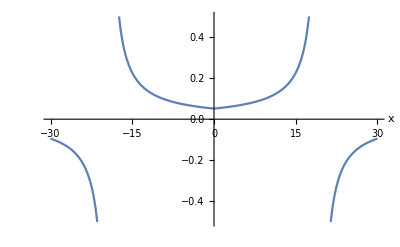

```mathematica
Plot[Vring[x,0,19.43],{x,-30,30},AxesLabel->Automatic ,PlotLegends->Automatic,PlotRange->{-0.5,0.5},PlotPoints->100]
```

```mathematica
(*plots for VmI*)
(*-------------------------------------------------------------------------------------------------------------*)
```

```mathematica
DensityPlot[ VmI[x,y,0,0]/2,{x,-25,25},{y,-25,25},AxesLabel->Automatic ,PlotLegends->Automatic,PlotRange->{-0.12,0.12},PlotPoints-> 300, Frame->True, FrameTicksStyle->Directive[Black,20]]
```

-Graphics-

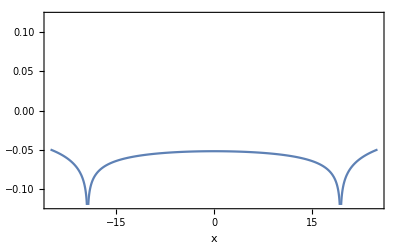

```mathematica
Plot[ VmI[x,0,0,0]/2,{x,-25,25},AxesLabel->Automatic ,PlotLegends->Automatic,PlotRange->{-0.12,0.12},PlotPoints-> 300, Frame->True, FrameTicksStyle->Directive[Black,20]]
```

```mathematica
DensityPlot[VmI[x,y,0,1],{x,-25,25},{y,-25,25},AxesLabel->Automatic ,PlotLegends->Automatic,PlotRange->{-0.12,0.12},PlotPoints-> 300,Frame->True, FrameTicksStyle->Directive[Black,20] ]
```

-Graphics-